# Comparison between the triangle plaquette model and the triangle continuum model.

# Triangular Plaquette Model H = (2/g^2) E^2 + 2/g^2 B^2 ---> (2/g^2)(E1^2 +E2^2 + E3^2) + (1/g^2) (1 - Cos[theta1, +theta2 + theta3)) With commutators [E_i, e^{itheta_j}] = delta_[ij} e^{itheta_j}

```mathematica
(* All terms are positve: With Wilson Plaq
B^2(s) = (1/2)Tr[2 - U_p - U^\dag_p](s) 
 (B(s)_etra)^2 = \sum_s Tr[2 - U(s)U^\dag(s+1) - U(s+1)U^\dag(s)] 

For U(1) Qubits Links:    U      --> sigma^+ = (sigma^x + i sigma^y)/2
                        U^\dag --> sigma^- = (sigma^x - i sigma^y)/2

E(s) = sigma^z(s) +  sigma^z(s+1)

Conventions for Qubit kernel construction *)
```

```mathematica
(*Sigma operators*)
```

```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
SigmaP= (Sigma[1]+ I*Sigma[2])/2;
SigmaM= (Sigma[1]- I*Sigma[2])/2;
```

```mathematica
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
```

```mathematica
(* Insert FullSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
FullSigma[ a_, j_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]
MatrixForm[FullSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
NQubits = 6
```

6

```mathematica
(*  zero point terms ((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit]*)
```

## Plaquette term

```mathematica
(*Single plaquette term at s-th layer *)
```

{4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,0}

{6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}

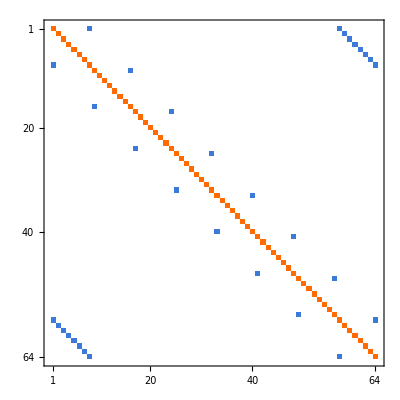

```mathematica
Bsingle[s_, nQubit_] :=KroneckerProduct[ IdentityMatrix[2^(3*(s-1))],SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]];
(*Sum over all layers*)
B[nQubit_] := - Sum[Bsingle[s, nQubit],{s,1,nQubit/3}]  + (nQubit/3)  IdentityMatrix[2^nQubit]
Eigenvalues[B[6]]
Eigenvalues[B[9]]
MatrixPlot[B[6]]
```

## Electric links between neighborhood layers sigmaz_{j + 3} x sigmaz_j note + convention on Qubit operators

```mathematica
Es[nQubit_] :=   Sum[FullSigma[3,Mod[j+3,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] +  (nQubit - 6 Mod[nQubit,2])*IdentityMatrix[2^nQubit]
Eigenvalues[Es[3]]
```

{3,3,3,3,3,3,3,3}

## XX + YY chain

{24,20,20,20,20,20,20,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,0}

{24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,6,6,6,6,6,6,6,6}

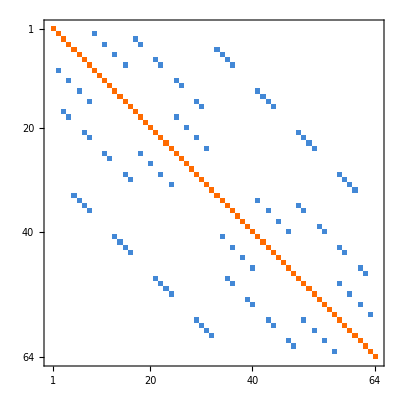

```mathematica
XY[nQubit_] :=- Sum[FullSigma[1,Mod[j+3,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]+
- Sum[FullSigma[2,Mod[j+3,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]  + 2 nQubit * IdentityMatrix[2^nQubit] 
Eigenvalues[XY[6]]
Eigenvalues[XY[9]]
MatrixPlot[XY[6]]
```

## Define Hamiltonian

```mathematica
(* Sign are choosen to be "right" of Hamilton *)
```

```mathematica
(* H0[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]
H1[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*H1s[nQubit]-  (alpha/(2*g^2))*H2s[nQubit] - (1/(2*g^2))*H3s[nQubit]]+
((g^2 /2) nQubit  + 2 (alpha/(2*g^2))nQubit + ((nQubit/3)/(2g^2))) IdentityMatrix[2^nQubit] *)
```

```mathematica
H[g_, alpha_, nQubit_]:=SparseArray[((g^2)/2)*Es[nQubit] + (1/(2*g^2))* B[nQubit]+  (alpha/(2*g^2))*XY[nQubit]]
```

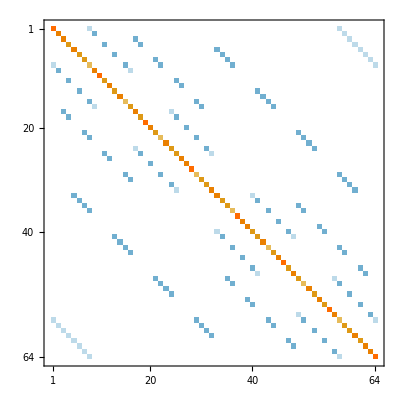

{0.97904,4.96887,4.96887,4.96887,4.96887,4.96887,4.96887,5.,5.,5.,8.82186,8.93845,8.93845,8.93845,8.93845,8.93845,8.93845,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.0311,13.0311,13.0311,13.0311,13.0311,13.0311,13.0616,13.0616,13.0616,13.0616,13.0616,13.0616,13.1991}

```mathematica
MatrixPlot[H[1, 1, 6]]
Sort[Eigenvalues[Normal[H[0.1, 1, 6]]]//N]
```

```mathematica
Eigenvalues[B[6]]
```

{4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,0}

```mathematica
Eigenvalues[XY[6]]
```

{24,20,20,20,20,20,20,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,4,4,4,4,4,4,0}

```mathematica
MatrixPlot[H[1, 1, 6]]
```

-Graphics-

## Eigenvalue spectrum of H(g, alpha)

```mathematica
Eigs[g_, alpha_, nQubit_, k_] := Sort[Eigenvalues[H[g, alpha, nQubit], k], Less]
```

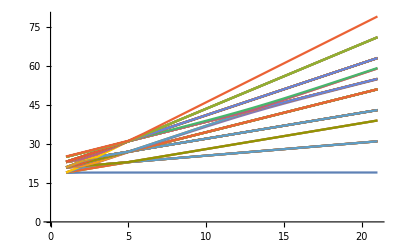

```mathematica
ListPlot[Transpose[Table[Eigs[1, c, 6, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

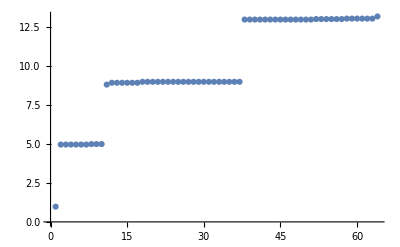

```mathematica
ListPlot[Eigs[1, 1,6 , 2^6]]
```

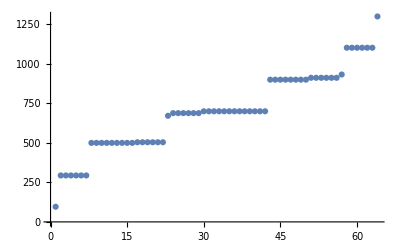

```mathematica
ListPlot[Eigs[0.1, 1,6 , 2^6]]
```

# Gauge Rotation Operators

```mathematica
(* Gauge Rotation Operators J12, J23, J31 *)
J12[nQubit_] := Sum[FullSigma[3,Mod[s*3+1,nQubit], nQubit]-FullSigma[3, Mod[s*3+2,nQubit], nQubit],{s,0,nQubit/3-1}]
J23[nQubit_] := Sum[FullSigma[3,Mod[s*3+2,nQubit], nQubit]-FullSigma[3, Mod[s*3+3,nQubit], nQubit],{s,0,nQubit/3-1}]
J31[nQubit_] := Sum[FullSigma[3,Mod[s*3+3,nQubit], nQubit]-FullSigma[3, Mod[s*3+1,nQubit], nQubit],{s,0,nQubit/3-1}]
```

## Eigenvalues (Diagonal Elements) of Gauge Rotation Operators

```mathematica
D12 = Normal[Diagonal[J12[NQubits]]];
```

```mathematica
D23 = Normal[Diagonal[J23[NQubits]]];
```

```mathematica
D31 = Normal[Diagonal[J31[NQubits]]];
```

```mathematica
(*Check if they sum up to zero *)
```

```mathematica
D12 + D23 + D31;
```

```mathematica
Sort[D12^2+  D23 ^2 + D31^2];
```

## Permutation Rule Ordered by Square Sum Eigenvalues

```mathematica
perm = Ordering[D12^2+ D23^2+D31^2];
```

```mathematica
(* Count the number of zeros *)
```

```mathematica
NZero = Count[D12^2+ D23^2+D31^2, 0]
```

10

## The Permutated Hamiltonian Looks It Consists of Block Sectors with Sub-square Matrices

```mathematica
PermHamiltonian[g_, alpha_, nQubits_] := H[g, alpha, nQubits][[perm, perm]]
```

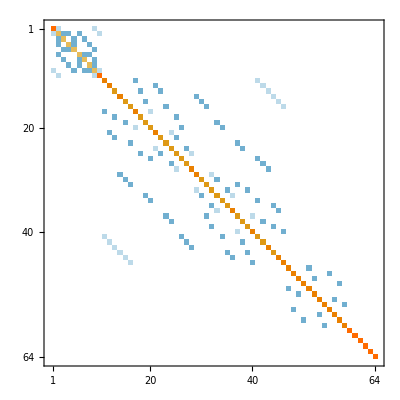

```mathematica
MatrixPlot[PermHamiltonian[1, 1, NQubits]]
```

## The sub matrix with basis corresponding to zero eigenvalues

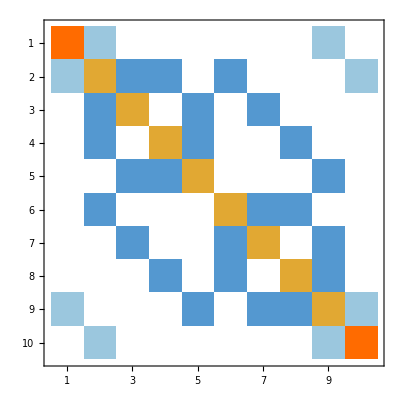

```mathematica
ZeroHamiltonian[g_, alpha_, nQubits_]  := PermHamiltonian[g, alpha, nQubits][[1;;NZero, 1;;NZero]]
ZeroH11 = ZeroHamiltonian[0.1, 1, NQubits];
MatrixPlot[ZeroH11]
```

## Eigenvalue Spectrum of the Sub-Hamiltonian

```mathematica
EigenSort11= Sort[N[Eigenvalues[Normal[ZeroH11]]]]
```

{0.97904,5.,5.,5.,8.82186,9.,9.,13.,13.,13.1991}

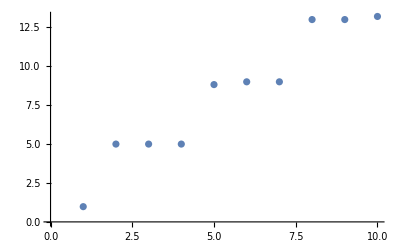

```mathematica
ListPlot[EigenSort11]
```

```mathematica
ListPlot[EigenSort11[[1;;64]]]
```

Part::take: Cannot take positions 1 through 64 in {0.97904,5.,5.,5.,8.82186,9.,9.,13.,13.,13.1991}.

ListPlot::lpn: {0.97904,5.,5.,5.,8.82186,9.,9.,13.,13.,13.1991}⟦1;;64⟧ is not a list of numbers or pairs of numbers.

ListPlot[{0.97904,5.,5.,5.,8.82186,9.,9.,13.,13.,13.1991}⟦1;;64⟧]

## What if we change the value of g?

```mathematica
EigenSpectra011:= Sort[Eigenvalues[ZeroHamiltonian[0.1, 1.0, NQubits]]]
(* EigenSpectra//N *) 
lambda0= EigenSpectra011[[1]]//N
lambda1 = EigenSpectra011[[2]]//N
EigenSpectraScaled011 = (1/(lambda1 - lambda0))( EigenSpectra011+ lambda1 - 2 lambda0)//N
```

95.7979

500.

{1.,2.,2.,2.,2.42453,2.49495,2.9896,2.9896,3.07042,3.97921}

```mathematica
ListPlot[EigenSpectraScaled011[[1;;64]]]
```

Part::take: Cannot take positions 1 through 64 in {1.,2.,2.,2.,2.42453,2.49495,2.9896,2.9896,3.07042,3.97921}.

ListPlot::lpn: {1.,2.,2.,2.,2.42453,2.49495,2.9896,2.9896,3.07042,3.97921}⟦1;;64⟧ is not a list of numbers or pairs of numbers.

ListPlot[{1.,2.,2.,2.,2.42453,2.49495,2.9896,2.9896,3.07042,3.97921}⟦1;;64⟧]

# 1D chain XXZ model (I.e. No plaquette term)

## The X term and Y term have the same coefficient: H = \sum_j Jxy*X_jX_{j+1} + Jxy*Y_jY_{j+1} + J_z*Z_jZ_{j+1}

```mathematica
XXZ[jxy_, jz_, nQubit_]:= -jxy*(Sum[FullSigma[1,Mod[j+1,nQubit], nQubit].FullSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] + Sum[FullSigma[2,Mod[j+1,nQubit], nQubit].FullSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}] ) -jz*Sum[FullSigma[3,Mod[j+1,nQubit], nQubit].FullSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

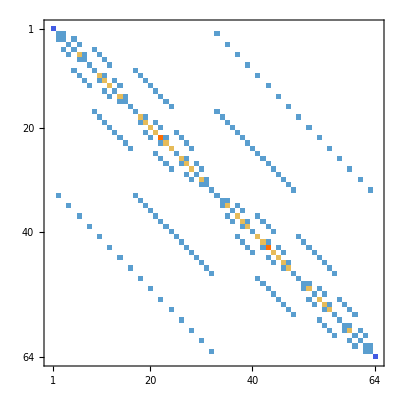

```mathematica
MatrixPlot[XXZ[1, 1, 6]]
```

```mathematica
{evals,evecs}=Eigensystem[XXZ[0.01, 1, 6]];
sortedEigs = SortBy[Transpose[{evals,evecs}],First];
sortedEigs[[1, 2]]
BaseForm[Position[sortedEigs[[1, 2]], _?(Abs[#]>0.01&)], 2]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}

{{1000000_2}}

# Continuum Model Change varables preserving the computors (and redefing charge!) H = (2/g^2)p^2 + (1/g^2) (1 - Cos[theta]) + p12^2 +p23^2 + p31^2 with theta = theta1, +theta2 + theta3 and p = (E1 +E2 + E3)/ 3 External flux/gauge opeartors pij = E_i - E_j

```mathematica
Dia[n_]:= Table[i^2,{i,-n,n}]
Dia[5]
```

{25,16,9,4,1,0,1,4,9,16,25}

# This initializs the matrix for one plaquette, where a is the strength of the magnetic part relative to electric part.

```mathematica
Mat[n_,g_]:=
Table[ (g^2/2)KroneckerDelta[i,j] i^2+ (1/g^2)( 2 KroneckerDelta[i,j] -  KroneckerDelta[i,j+1]-KroneckerDelta[i,j-1]),{i,-n,n},{j,-n,n}]
MatrixForm[Mat[4,g]]
```

(2/g^2+8 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/g^2 | 2/g^2 | -1/g^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+g^2/2 | -1/g^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+2 g^2 | -1/g^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+(9 g^2)/2 | -1/g^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/g^2 | 2/g^2+8 g^2)

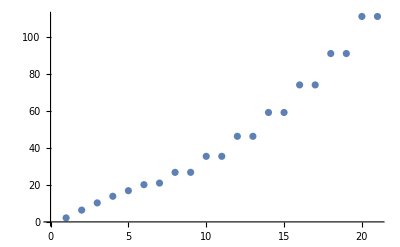

```mathematica
ListPlot[Sort[Re[Eigenvalues[(2/0.795^2)Mat[10,0.795]]],Less]]
```

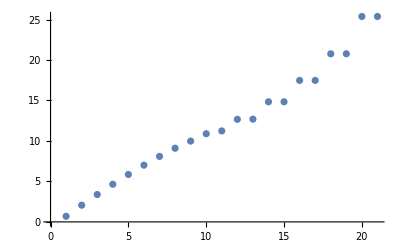

```mathematica
ListPlot[Sort[Re[Eigenvalues[Mat[10,0.6]]],Less]]
```

```mathematica
Dat=Table[Sort[Re[Eigenvalues[Mat[18,g], Method->"Banded"]],Less],{g,0.1,2.1,0.05}];
```

```mathematica
Here one can see how the level degenracy is split as we increase the magnetic term
as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]
```

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.35,-71.08}]

as can degenracy how increase is level magnetic one see split term the^2 we GeoPosition[{42.37,-71.13}]

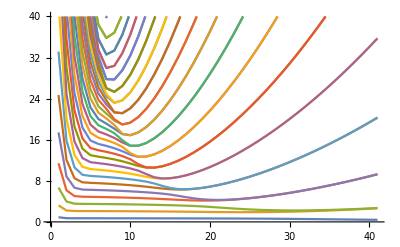

```mathematica
ListPlot[Transpose[Dat], Joined->True,PlotRange->{0,40}]
```

```mathematica
Length[Dat]
```

41

```mathematica
Here is the result with plaquette = 0 and with plaquette = 20, showing that the low energy degrees of freedom have a linear spectrum once magnetic term is strong
```

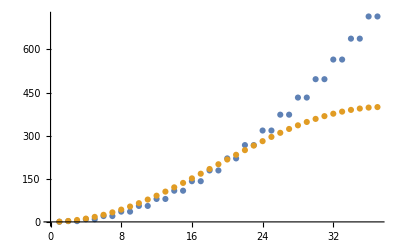

```mathematica
ListPlot[{Dat[[41]],Dat[[1]]}]
```

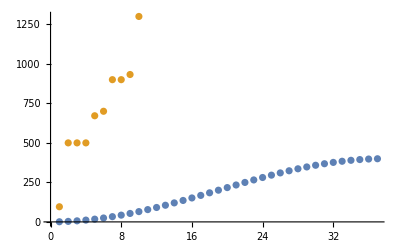

```mathematica
ListPlot[{Dat[[1]], Sort[Eigenvalues[ZeroHamiltonian[0.1, 1, 6]]]}]
```